# Solving and Simulating RBC Models with Mathematica

Diallo Ibrahima Amadou*
Clermont University, University of Auvergne, Centre d’Études et de Recherches sur le Développement International, CERDI-CNRS, 65, bd François Mitterrand, 63000 Clermont-Ferrand, France. 
Contact: zavren@gmail.com
September 2012

Abstract

This notebook illustrates how to solve and simulate a Real Business Cycle (RBC) model using Mathematica. It starts from finding the first order conditions, then derives the steady-state, log-linearizes and solves the RBC model. After solving the model, the notebook first computes the impulse response functions and then simulates the model. It ends by calculating some second moments statistics of the RBC model. When we want to solve a RBC model, soon or later, we will need to use a software. This notebook demonstrates how to do this using Mathematica without having the need to use paper and pencil to derive the equilibrium conditions and log-linearize the model first, and then use a numerical software to perform the simulations. In this notebook, all these steps are done with Mathematica and fully explained in detail.

Keywords: real business cycle; steady-state; log-linearization; simulation; impulse response functions; second moments statistics; dynamic stochastic general equilibrium models

JEL Classification: C6, E2, O3

*All comments are welcome. All Errors and inaccuracies are mine.

## 1. Introduction

Real Business Cycle (RBC) models have become the basic workhorse of Dynamic Stochastic General Equilibrium Models (DSGE). DSGE models themselves are now being used both by researchers and professionals, including central bankers, to study and forecast short term economic fluctuations. The hoped contribution of the notebook is the illustration of how to solve and simulate RBC models using Mathematica. Before starting, it is important to inform the reader that this notebook is written with Mathematica 8.0 in a Windows 7 machine. Thus the notebook may or may not work well in future versions of Mathematica.

## 2. Defining the Model

We load the PlotLegends package. This package allows us to make legends for graphs further below.

```mathematica
<<PlotLegends`
```

We present a modified version of the Hansen (1985) RBC model. The social planner’s maximization problem can be written as:

Max E_0[∑_(t=0)^∞ β^t((c_t^(1-θ)-1)/(1-θ)-ψ l_t^(1+γ)/(1+γ))]
Subject to:
c_t+iv_t=y_t
       y_t=z_t k_t^α l_t^(1-α)
       k_(t+1)=(1-δ) k_t+iv_t
       Log[z_(t+1)]=(1-ρ) Log[zs]+ρ Log[z_t]+ϵ_(t+1)
       k_0 and z_0 are given

Where:
E_0[·] is the expectations operator
  β ∈ (0,1) is the discount factor
  c_t is the consumption
  1/θ measures the constant intertemporal elasticity of substitution in consumption. We have θ >0
  γ represents the inverse of the Frisch intertemporal elasticity of substitution in labour supply. We have γ≥0
  l_t is labor 
  ψ indicates the disutility weight given to labor in the utility function. We have ψ>0
  iv_t is investment. We denote investment by iv_t since I is a reserved word in Mathematica
  y_t is output
  k_t is capital at period t and k_(t+1) is capital at t+1
  δ ∈ (0,1) is the capital depreciation rate 
  z_t is the exogenous technology shock. zs is the steady-state level of z_t
  ρ ∈ [0,1] is the autocorrelation parameter of technology
  ϵ_(t+1) the innovations to technology
  ϵ_t∼^iid N(0,σ^2)
  t indicates the time.

The model presented here results to the Hansen (1985) model when θ and γ tend towards 1 and 0 respectively. Let’s illustrate this:
First we take the limit of the utility function when θ goes towards 1

```mathematica
ssrbcmod1=Limit[(Subscript[c, t]^(1-θ)-1)/(1-θ)-ψ Subscript[l, t]^(1+γ)/(1+γ),θ->1]
```

((1+γ) Log[c_t]-ψ l_t^(1+γ))/(1+γ)

Then we take the limit of the result when γ approaches 0.

```mathematica
ssrbcmod2=Limit[ssrbcmod1,γ->0]
```

Log[c_t]-ψ l_t

This last expression is the utility function used in the Hansen (1985) RBC model. The only difference is that l_t represents there leisure instead of labor supply. Also the minus sign becomes a positive sign since we are dealing there with leisure.

Next we illustrate how the budget constraint is obtained. We first enter the equation of motion of capital stock.

```mathematica
ssrbcmod3=Subscript[k, t+1]==(1-δ) Subscript[k, t]+Subscript[iv, t]
```

k_(1+t)==iv_t+(1-δ) k_t

We enter the identity stating that consumption plus investment is equal to output.

```mathematica
ssrbcmod4=Subscript[c, t]+Subscript[iv, t]==Subscript[y, t]
```

c_t+iv_t==y_t

We solve for investment in the previous identity.

```mathematica
ssrbcmod5=Solve[ssrbcmod4,Subscript[iv, t]][[1,1]]
```

iv_t→-c_t+y_t

We substitute investment in the equation of motion of capital.

```mathematica
ssrbcmod6=ssrbcmod3/.ssrbcmod5
```

k_(1+t)==-c_t+(1-δ) k_t+y_t

We replace output by its value. Hence the budget constraint.

```mathematica
ssrbcmod7=ssrbcmod6/. Subscript[y, t]->Subscript[z, t] Subscript[k, t]^α Subscript[l, t]^(1-α)
```

k_(1+t)==-c_t+(1-δ) k_t+k_t^α l_t^(1-α) z_t

## 2.1. The Bellman Equation

The Bellman equation is
v[k_t,z_t]=Max_(c_t,k_(t+1),l_t){(c_t^(1-θ)-1)/(1-θ)-ψ l_t^(1+γ)/(1+γ)+β EX_t[v[k_(t+1),z_(t+1)]]}
Subject to:
The economy resource constraint: k_(1+t)=-c_t+(1-δ) k_t+l_t^(1-α) k_t^α z_t
       And technology:  Log[z_(t+1)]=(1-ρ) Log[zs]+ρ Log[z_t]+ϵ_(t+1)
We denote the expectations operator as EX_t[·]since E is a reserved word in Mathematica.

We enter the left hand side of the Bellman equation

```mathematica
ssrbcmod8=v[Subscript[k, t],Subscript[z, t]]
```

v[k_t,z_t]

We enter the right hand side of the Bellman equation without the Max operator.

```mathematica
ssrbcmod9=(Subscript[c, t]^(1-θ)-1)/(1-θ)-ψ Subscript[l, t]^(1+γ)/(1+γ)+β Subscript[EX, t][v[Subscript[k, t+1],Subscript[z, t+1]]]
```

(-1+c_t^(1-θ))/(1-θ)-(ψ l_t^(1+γ))/(1+γ)+β EX_t[v[k_(1+t),z_(1+t)]]

We enter the technology equation

```mathematica
ssrbcmod10=Log[Subscript[z, t+1]]==(1-ρ) Log[zs]+ρ Log[Subscript[z, t]]+Subscript[ϵ, t+1]
```

Log[z_(1+t)]==(1-ρ) Log[zs]+ρ Log[z_t]+ϵ_(1+t)

We enter the right hand side of the Bellman equation without the expectations operator.

```mathematica
ssrbcmod11=(Subscript[c, t]^(1-θ)-1)/(1-θ)-ψ Subscript[l, t]^(1+γ)/(1+γ)+β v[Subscript[k, t+1],Subscript[z, t+1]]
```

(-1+c_t^(1-θ))/(1-θ)-(ψ l_t^(1+γ))/(1+γ)+β v[k_(1+t),z_(1+t)]

We isolate consumption in the resource constraint.

```mathematica
ssrbcmod12=ssrbcmod7[[1]]-Subscript[k, 1+t]==ssrbcmod7[[2]]-Subscript[k, 1+t]
```

0==-c_t+(1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t

```mathematica
ssrbcmod13=ssrbcmod12[[1]]+Subscript[c, t]==ssrbcmod12[[2]]+Subscript[c, t]
```

c_t==(1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t

We substitute consumption by its value in the right hand side of the Bellman Equation.

```mathematica
ssrbcmod14=ssrbcmod11/.ssrbcmod13[[1]]->ssrbcmod13[[2]]
```

-(ψ l_t^(1+γ))/(1+γ)+(-1+((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^(1-θ))/(1-θ)+β v[k_(1+t),z_(1+t)]

We take the derivative of this last expression with respect to k_(t+1) and set it equal to 0.

```mathematica
ssrbcmod15=D[ssrbcmod14,Subscript[k, t+1]]==0
```

-((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^-θ+β v^(1,0)[k_(1+t),z_(1+t)]==0

We take the derivative of the right hand side of the Bellman Equation with respect to l_t and set it equal to 0.

```mathematica
ssrbcmod16=D[ssrbcmod14,Subscript[l, t]]==0
```

-ψ l_t^γ+(1-α) k_t^α l_t^-α z_t ((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^-θ==0

The Benveniste-Scheinkman envelope theorem condition is given by

```mathematica
ssrbcmod17=D[ssrbcmod8,Subscript[k, t]]==D[ssrbcmod14,Subscript[k, t]]
```

v^(1,0)[k_t,z_t]==(1-δ+α k_t^(-1+α) l_t^(1-α) z_t) ((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^-θ

We forward t by one period in the preceding equation.

```mathematica
ssrbcmod18=ssrbcmod17/.t->t+1
```

v^(1,0)[k_(1+t),z_(1+t)]==(1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t)) ((1-δ) k_(1+t)-k_(2+t)+k_(1+t)^α l_(1+t)^(1-α) z_(1+t))^-θ

We take expections into account in equation ssrbcmod15

```mathematica
ssrbcmod19=ssrbcmod15/.Derivative[1,0][v][Subscript[k, 1+t],Subscript[z, 1+t]]->Subscript[EX, t][Derivative[1,0][v][Subscript[k, 1+t],Subscript[z, 1+t]]]
```

-((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^-θ+β EX_t[v^(1,0)[k_(1+t),z_(1+t)]]==0

We substitute v^(1,0)[k_(1+t),z_(1+t)] by its value in the previous equation.

```mathematica
ssrbcmod20=ssrbcmod19/.ssrbcmod18[[1]]->ssrbcmod18[[2]]
```

-((1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t)^-θ+β EX_t[(1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t)) ((1-δ) k_(1+t)-k_(2+t)+k_(1+t)^α l_(1+t)^(1-α) z_(1+t))^-θ]==0

Remember that consumption is given by

```mathematica
ssrbcmod21=ssrbcmod13
```

c_t==(1-δ) k_t-k_(1+t)+k_t^α l_t^(1-α) z_t

We forward t by one period in the preceding equation.

```mathematica
ssrbcmod22=ssrbcmod21/.t->t+1
```

c_(1+t)==(1-δ) k_(1+t)-k_(2+t)+k_(1+t)^α l_(1+t)^(1-α) z_(1+t)

We replace the right hand sides of ssrbcmod21 and ssrbcmod22 by c_t and c_(t+1) respectively in equation ssrbcmod20.

```mathematica
ssrbcmod23=ssrbcmod20/.{ssrbcmod21[[2]]->ssrbcmod21[[1]],ssrbcmod22[[2]]->ssrbcmod22[[1]]}
```

-c_t^-θ+β EX_t[c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))]==0

This last equation is known as the Euler equation. It is also called Lucas asset pricing equation. We rewrite it without the expectations operator. But we keep in mind that there is always an expectation operator for this equation.

```mathematica
ssrbcmod24=ssrbcmod23/.Subscript[EX, t][Subscript[c, 1+t]^-θ (1-δ+α Subscript[k, 1+t]^(-1+α) Subscript[l, 1+t]^(1-α) Subscript[z, 1+t])]->Subscript[c, 1+t]^-θ (1-δ+α Subscript[k, 1+t]^(-1+α) Subscript[l, 1+t]^(1-α) Subscript[z, 1+t])
```

-c_t^-θ+β c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))==0

Now, we replace c_t by its value in equation ssrbcmod16

```mathematica
ssrbcmod25=ssrbcmod16/.ssrbcmod21[[2]]->ssrbcmod21[[1]]
```

-ψ l_t^γ+(1-α) c_t^-θ k_t^α l_t^-α z_t==0

We solve for c_t in the previous equation

```mathematica
ssrbcmod26=Solve[ssrbcmod25,Subscript[c, t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c_t→((l_t^-γ (k_t^α l_t^-α z_t-α k_t^α l_t^-α z_t))/ψ)^(1/θ)}}

We transform this expression to an equation for convenience

```mathematica
ssrbcmod27=ssrbcmod26[[1,1,1]]==ssrbcmod26[[1,1,2]]
```

c_t==((l_t^-γ (k_t^α l_t^-α z_t-α k_t^α l_t^-α z_t))/ψ)^(1/θ)

This last equation represents the labor-leisure choice equation. We expand the powers in this equation to get:

```mathematica
ssrbcmod28=PowerExpand[ssrbcmod27]
```

c_t==ψ^(-1/θ) l_t^(-γ/θ) (k_t^α l_t^-α z_t-α k_t^α l_t^-α z_t)^(1/θ)

## 2.2. The Steady-State Equilibrium

Now we derive the steady-state equilibrium for the main variables. We start with the Euler equation.

```mathematica
ssrbcmod29=ssrbcmod23
```

-c_t^-θ+β EX_t[c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))]==0

We define steady-state variables by adding an s to the existing variables. For example the steady-state consumption is noted as cs for consumption star.

```mathematica
ssrbcmod30=ssrbcmod29/.{Subscript[c, t]->cs,Subscript[c, t+1]->cs,Subscript[k, t+1]->ks,Subscript[l, t+1]->ls,Subscript[z, t+1]->zs}
```

-cs^-θ+β EX_t[cs^-θ (1+ks^(-1+α) ls^(1-α) zs α-δ)]==0

By the definition of steady-steady, all variables are constant. Hence their expectations are themselves. Thus we have.

```mathematica
ssrbcmod31=ssrbcmod30/.Subscript[EX, t][cs^-θ (1+ks^(-1+α) ls^(1-α) zs α-δ)]->cs^-θ (1+ks^(-1+α) ls^(1-α) zs α-δ)
```

-cs^-θ+cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ)==0

Also at the steady-state, there is no uncertainty, thus zs = 1.

```mathematica
ssrbcmod32=ssrbcmod31/.zs->1
```

-cs^-θ+cs^-θ β (1+ks^(-1+α) ls^(1-α) α-δ)==0

We divide this last equation by cs^-θ

```mathematica
ssrbcmod33=Expand[ssrbcmod32[[1]]/cs^-θ==ssrbcmod32[[2]]/cs^-θ]
```

-1+β+ks^(-1+α) ls^(1-α) α β-β δ==0

We define the following ratio

```mathematica
ssrbcmod34=Solve[ks/ls==kls,ks][[1,1]]
```

ks→kls ls

We substitute ks by its value in ssrbcmod33

```mathematica
ssrbcmod35=ssrbcmod33/.ssrbcmod34//PowerExpand
```

-1+β+kls^(-1+α) α β-β δ==0

We solve for kls in the previous equation.

```mathematica
ssrbcmod36=Solve[ssrbcmod35,kls][[1,1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

kls→(-(-1+β-β δ)/(α β))^(1/(-1+α))

We transform this result to an equation.

```mathematica
ssrbcmod37=ssrbcmod36[[1]]==ssrbcmod36[[2]]
```

kls==(-(-1+β-β δ)/(α β))^(1/(-1+α))

Now we turn to the labor-leisure choice equation.

```mathematica
ssrbcmod38=ssrbcmod28
```

c_t==ψ^(-1/θ) l_t^(-γ/θ) (k_t^α l_t^-α z_t-α k_t^α l_t^-α z_t)^(1/θ)

We define the steady-state variables for this equation.

```mathematica
ssrbcmod39=ssrbcmod38/.{Subscript[c, t]->cs,Subscript[l, t]->ls,Subscript[k, t]->ks,Subscript[z, t]->zs}
```

cs==ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ)

We set zs = 1

```mathematica
ssrbcmod40=ssrbcmod39/.zs->1
```

cs==ls^(-γ/θ) (ks^α ls^-α-ks^α ls^-α α)^(1/θ) ψ^(-1/θ)

We substitute ks by its value

```mathematica
ssrbcmod41=ssrbcmod40/.ssrbcmod34//PowerExpand
```

cs==ls^(-γ/θ) (kls^α-kls^α α)^(1/θ) ψ^(-1/θ)

We replace kls by its value.

```mathematica
ssrbcmod42=ssrbcmod41/.ssrbcmod36
```

cs==ls^(-γ/θ) (((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α-α ((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ)

We turn to the resource constraint.

```mathematica
ssrbcmod43=ssrbcmod7
```

k_(1+t)==-c_t+(1-δ) k_t+k_t^α l_t^(1-α) z_t

```mathematica
ssrbcmod44=ssrbcmod43/.{Subscript[k, t+1]->ks,Subscript[c, t]->cs,Subscript[k, t]->ks,Subscript[l, t]->ls,Subscript[z, t]->1}
```

ks==-cs+ks^α ls^(1-α)+ks (1-δ)

We divide by ks.

```mathematica
ssrbcmod45=Map[1/ks #&,ssrbcmod44]//Expand
```

1==1-cs/ks+ks^(-1+α) ls^(1-α)-δ

We substitute ks by its value.

```mathematica
ssrbcmod46=ssrbcmod45/.ssrbcmod34//PowerExpand
```

1==1+kls^(-1+α)-cs/(kls ls)-δ

We replace kls and cs by their values.

```mathematica
ssrbcmod47=ssrbcmod46/.{ssrbcmod36,ssrbcmod42[[1]]->ssrbcmod42[[2]]}
```

1==1-δ+((-(-1+β-β δ)/(α β))^(1/(-1+α)))^(-1+α)-ls^(-1-γ/θ) (-(-1+β-β δ)/(α β))^(-1/(-1+α)) (((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α-α ((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ)

We solve for ls in the previous equation.

```mathematica
ssrbcmod48=Solve[ssrbcmod47,ls]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ls→((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))}}

We change this to an equation.

```mathematica
ssrbcmod49=ssrbcmod48[[1,1,1]]==ssrbcmod48[[1,1,2]]
```

ls==((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))

We find the value of cs.

```mathematica
ssrbcmod50=ssrbcmod42/.ssrbcmod49[[1]]->ssrbcmod49[[2]]
```

cs==(((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α-α ((-(-1+β-β δ)/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ) (((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(-γ/θ)

```mathematica
ssrbcmod51=FullSimplify[ssrbcmod50]
```

cs==(-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ) (((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(-γ/θ)

We recall the value of ks.

```mathematica
ssrbcmod52=ssrbcmod34
```

ks→kls ls

We write this as an equation.

```mathematica
ssrbcmod53=ssrbcmod52[[1]]==ssrbcmod52[[2]]
```

ks==kls ls

We then find the value of ks.

```mathematica
ssrbcmod54=ssrbcmod53/.{ssrbcmod36,ssrbcmod49[[1]]->ssrbcmod49[[2]]}
```

ks==(-(-1+β-β δ)/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))

```mathematica
ssrbcmod55=FullSimplify[ssrbcmod54]
```

ks==((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))

Next we find the value of ys.

```mathematica
ssrbcmod56=Subscript[y, t]==Subscript[z, t] Subscript[k, t]^α Subscript[l, t]^(1-α)
```

y_t==k_t^α l_t^(1-α) z_t

```mathematica
ssrbcmod57=ssrbcmod56/.{Subscript[y, t]->ys,Subscript[z, t]->zs,Subscript[k, t]->ks,Subscript[l, t]->ls}
```

ys==ks^α ls^(1-α) zs

We replace ks, ls and zs by their respective values.

```mathematica
ssrbcmod58=ssrbcmod57/.{ssrbcmod55[[1]]->ssrbcmod55[[2]],ssrbcmod49[[1]]->ssrbcmod49[[2]],zs->1}
```

ys==(((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(1-α) (((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^α

```mathematica
ssrbcmod59=FullSimplify[ssrbcmod58]
```

ys==(((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(1-α) (((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^α

We recall the expression of iv_t.

```mathematica
ssrbcmod60=ssrbcmod5
```

iv_t→-c_t+y_t

We transform this expression to an equation.

```mathematica
ssrbcmod61=ssrbcmod60[[1]]==ssrbcmod60[[2]]
```

iv_t==-c_t+y_t

We find the value of ivs.

```mathematica
ssrbcmod62=ssrbcmod61/.{Subscript[iv, t]->ivs,Subscript[c, t]->cs,Subscript[y, t]->ys}
```

ivs==-cs+ys

We replace cs and ys by their respective values.

```mathematica
ssrbcmod63=ssrbcmod62/.{ssrbcmod51[[1]]->ssrbcmod51[[2]],ssrbcmod59[[1]]->ssrbcmod59[[2]]}
```

ivs==-(-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ) (((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(-γ/θ)+(((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(1-α) (((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^α

## 3. Log-Linearization

Log-linearization is a mean of transforming the dynamic nonlinear equations to dynamic linear equations. This makes the calculations and interpretations easier. To do the log-linearization, we will write a variable x_t as xs ⅇ^xh_t, where xs is the steady-state value of x_t and xh_t=Log[x_t/xs]. This last expression is approximately the percentage deviation of x_t around the steady-state xs. In fact:

```mathematica
ssrbcmod64=Subscript[xh, t]==Series[Log[Subscript[x, t]/xs],{Subscript[x, t],xs,1}]//Normal
```

xh_t==(-xs+x_t)/xs

The h in xh_t is put for x hat. At the steady-state, we can verify that xh_t=(-xs+x_t)/xs=0. In fact at the steady-state xh_t=(-xs+xs)/xs=0. We can check that the expression xs ⅇ^xh_t gives the original variable x_t by calculating:

```mathematica
ssrbcmod65=xs ⅇ^Subscript[xh, t]/.Subscript[xh, t]->Log[Subscript[x, t]/xs]
```

x_t

More log-linearization techniques can be found in Uhlig (1997) and Zietz (2008). Now let's start the log-linearization of the key equilibrium equations.

## 3.1. The Labor-Leisure Choice Equation

Let's write a function that performs multivariate linear Taylor series approximation. The function takes three arguments. The first represents the mathematical function we want to linearize. The second is the list of variables with respect to which we want to linearize and the third argument is the list of points around which we want to take the linearization.

```mathematica
mulLinearTaylor[f_,x_,a_]:=Module[{fa,gradf,gradfa},fa=f//.Thread[x->a];gradf=D[f,{x}];gradfa=gradf//.Thread[x->a];fa+gradfa.(x-a)]
```

We recall the labor-leisure choice equation.

```mathematica
ssrbcmod66=ssrbcmod28
```

c_t==ψ^(-1/θ) l_t^(-γ/θ) (k_t^α l_t^-α z_t-α k_t^α l_t^-α z_t)^(1/θ)

We first replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod67=ssrbcmod66/.{Subscript[c, t]->cs ⅇ^Subscript[ch, t],Subscript[l, t]->ls ⅇ^Subscript[lh, t],Subscript[k, t]->ks ⅇ^Subscript[kh, t],Subscript[z, t]->zs ⅇ^Subscript[zh, t]}
```

cs ⅇ^ch_t==(ⅇ^lh_t ls)^(-γ/θ) (ⅇ^zh_t (ⅇ^kh_t ks)^α (ⅇ^lh_t ls)^-α zs-ⅇ^zh_t (ⅇ^kh_t ks)^α (ⅇ^lh_t ls)^-α zs α)^(1/θ) ψ^(-1/θ)

We take the first order Taylor series approximation of the left hand side of this equation with respect to ch_t around 0.

```mathematica
ssrbcmod68=Series[ssrbcmod67[[1]],{Subscript[ch, t],0,1}]//Normal
```

cs+cs ch_t

We take the first order multivariate Taylor series approximation of the right hand side of equation ssrbcmod67 with respect to lh_t, zh_t and kh_t respectively around 0, 0 and 0.

```mathematica
ssrbcmod69=mulLinearTaylor[ssrbcmod67[[2]],{Subscript[lh, t],Subscript[zh, t],Subscript[kh, t]},{0,0,0}]
```

ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ)+(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (ks^α ls^-α zs α-ks^α ls^-α zs α^2) ψ^(-1/θ) kh_t)/θ+((ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (-ks^α ls^-α zs α+ks^α ls^-α zs α^2) ψ^(-1/θ))/θ-(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) γ ψ^(-1/θ))/θ) lh_t+(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ) zh_t)/θ

We equalize the two expressions ssrbcmod68 and ssrbcmod69 to form an equation.

```mathematica
ssrbcmod70=ssrbcmod68==ssrbcmod69
```

cs+cs ch_t==ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ)+(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (ks^α ls^-α zs α-ks^α ls^-α zs α^2) ψ^(-1/θ) kh_t)/θ+((ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (-ks^α ls^-α zs α+ks^α ls^-α zs α^2) ψ^(-1/θ))/θ-(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) γ ψ^(-1/θ))/θ) lh_t+(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ) zh_t)/θ

Now, we form the steady-state equation of the labor-leisure choice equation.

```mathematica
ssrbcmod71=ssrbcmod66/.{Subscript[c, t]->cs,Subscript[l, t]->ls,Subscript[k, t]->ks,Subscript[z, t]->zs}
```

cs==ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ)

We substract equation ssrbcmod71 from equation ssrbcmod70.

```mathematica
ssrbcmod72=ssrbcmod70[[1]]-ssrbcmod71[[1]]==ssrbcmod70[[2]]-ssrbcmod71[[2]]
```

cs ch_t==(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (ks^α ls^-α zs α-ks^α ls^-α zs α^2) ψ^(-1/θ) kh_t)/θ+((ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(-1+1/θ) (-ks^α ls^-α zs α+ks^α ls^-α zs α^2) ψ^(-1/θ))/θ-(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) γ ψ^(-1/θ))/θ) lh_t+(ls^(-γ/θ) (ks^α ls^-α zs-ks^α ls^-α zs α)^(1/θ) ψ^(-1/θ) zh_t)/θ

We divide equation ssrbcmod72 by equation ssrbcmod71.

```mathematica
ssrbcmod73=ssrbcmod72[[1]]/ssrbcmod71[[1]]==Apply[Plus,Table[FullSimplify[ssrbcmod72[[2,i]]/ssrbcmod71[[2]]],{i,1,Length[ssrbcmod72[[2]]]}]]
```

ch_t==(α kh_t)/θ-((α+γ) lh_t)/θ+zh_t/θ

This last equality represents the log-linearized equation of the labor-leisure choice equation. In traditional economic notation, this equation can be rewritten as:
(ĉ)_t=(α (k̂)_t)/θ-((α+γ) (l̂)_t)/θ+((ẑ)_t)/θ
Where a hat over a variable indicates percentage deviation of the variable around the steady-state.

## 3.2. The Euler Equation or Lucas Asset Pricing Equation

We recall the Euler equation without the expectations operator. We will put back this operator when we finish the log-linearization process.

```mathematica
ssrbcmod74=ssrbcmod24
```

-c_t^-θ+β c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))==0

We isolate c_t.

```mathematica
ssrbcmod75=ssrbcmod74[[1]]-β Subscript[c, 1+t]^-θ (1-δ+α Subscript[k, 1+t]^(-1+α) Subscript[l, 1+t]^(1-α) Subscript[z, 1+t])==ssrbcmod74[[2]]-β Subscript[c, 1+t]^-θ (1-δ+α Subscript[k, 1+t]^(-1+α) Subscript[l, 1+t]^(1-α) Subscript[z, 1+t])
```

-c_t^-θ==-β c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))

We multiply this last equality by -1.

```mathematica
ssrbcmod76=Map[-1 #&,ssrbcmod75]
```

c_t^-θ==β c_(1+t)^-θ (1-δ+α k_(1+t)^(-1+α) l_(1+t)^(1-α) z_(1+t))

We replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod77=ssrbcmod76/.{Subscript[c, t]->cs ⅇ^Subscript[ch, t],Subscript[c, t+1]->cs ⅇ^Subscript[ch, t+1],Subscript[k, t+1]->ks ⅇ^Subscript[kh, t+1],Subscript[l, t+1]->ls ⅇ^Subscript[lh, t+1],Subscript[z, t+1]->zs ⅇ^Subscript[zh, t+1]}
```

(cs ⅇ^ch_t)^-θ==(cs ⅇ^(ch_(1+t)))^-θ β (1+ⅇ^(zh_(1+t)) (ⅇ^(kh_(1+t)) ks)^(-1+α) (ⅇ^(lh_(1+t)) ls)^(1-α) zs α-δ)

We take the first order Taylor series approximation of the left hand side of this equation with respect to ch_t around 0.

```mathematica
ssrbcmod78=Series[ssrbcmod77[[1]],{Subscript[ch, t],0,1}]//Normal
```

cs^-θ-cs^-θ θ ch_t

We take the first order multivariate Taylor series approximation of the right hand side of equation ssrbcmod77 with respect to ch_(1+t), zh_(1+t), kh_(1+t) and lh_(1+t) respectively around 0, 0, 0 and 0.

```mathematica
ssrbcmod79=mulLinearTaylor[ssrbcmod77[[2]],{Subscript[ch, 1+t],Subscript[zh, 1+t],Subscript[kh, 1+t],Subscript[lh, 1+t]},{0,0,0,0}]
```

cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ)-cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ) θ ch_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (-1+α) α β kh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (1-α) α β lh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs α β zh_(1+t)

We equalize the two expressions ssrbcmod78 and ssrbcmod79 to form an equation.

```mathematica
ssrbcmod80=ssrbcmod78==ssrbcmod79
```

cs^-θ-cs^-θ θ ch_t==cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ)-cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ) θ ch_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (-1+α) α β kh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (1-α) α β lh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs α β zh_(1+t)

Now, we form the steady-state equation of the Euler equation.

```mathematica
ssrbcmod81=ssrbcmod76/.{Subscript[c, t]->cs,Subscript[c, t+1]->cs,Subscript[k, t+1]->ks,Subscript[l, t+1]->ls,Subscript[z, t+1]->zs}
```

cs^-θ==cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ)

We substract equation ssrbcmod81 from equation ssrbcmod80 side by side.

```mathematica
ssrbcmod82=ssrbcmod80[[1]]-ssrbcmod81[[1]]==ssrbcmod80[[2]]-ssrbcmod81[[2]]
```

-cs^-θ θ ch_t==-cs^-θ β (1+ks^(-1+α) ls^(1-α) zs α-δ) θ ch_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (-1+α) α β kh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs (1-α) α β lh_(1+t)+cs^-θ ks^(-1+α) ls^(1-α) zs α β zh_(1+t)

We divide both sides of the previous equation by -cs^-θ.

```mathematica
ssrbcmod83=ssrbcmod82[[1]]/-cs^-θ==Apply[Plus,Table[FullSimplify[ssrbcmod82[[2,i]]/-cs^-θ],{i,1,Length[ssrbcmod82[[2]]]}]]
```

θ ch_t==β (1+ks^(-1+α) ls^(1-α) zs α-δ) θ ch_(1+t)-ks^(-1+α) ls^(1-α) zs (-1+α) α β kh_(1+t)+ks^(-1+α) ls^(1-α) zs (-1+α) α β lh_(1+t)-ks^(-1+α) ls^(1-α) zs α β zh_(1+t)

We divide both sides of the steady-state equation by cs^-θ.

```mathematica
ssrbcmod84=Map[1/cs^-θ #&,ssrbcmod81]
```

1==β (1+ks^(-1+α) ls^(1-α) zs α-δ)

We rewrite this equation as:

```mathematica
ssrbcmod85=ssrbcmod84[[2]]==ssrbcmod84[[1]]
```

β (1+ks^(-1+α) ls^(1-α) zs α-δ)==1

This last equation implies that the log-linearized Euler equation is :

```mathematica
ssrbcmod86=ssrbcmod83/.ssrbcmod85[[1]]->ssrbcmod85[[2]]
```

θ ch_t==θ ch_(1+t)-ks^(-1+α) ls^(1-α) zs (-1+α) α β kh_(1+t)+ks^(-1+α) ls^(1-α) zs (-1+α) α β lh_(1+t)-ks^(-1+α) ls^(1-α) zs α β zh_(1+t)

We set zs = 1 in this last equation.

```mathematica
ssrbcmod87=ssrbcmod86/.zs->1
```

θ ch_t==θ ch_(1+t)-ks^(-1+α) ls^(1-α) (-1+α) α β kh_(1+t)+ks^(-1+α) ls^(1-α) (-1+α) α β lh_(1+t)-ks^(-1+α) ls^(1-α) α β zh_(1+t)

This last equation represents the log-linearized Euler equation without the expectations operator. This equality implies that the log-linearized Euler equation with the expectations operator is:

```mathematica
ssrbcmod88=ssrbcmod87/.{Subscript[ch, 1+t]->Subscript[EX, t][Subscript[ch, 1+t]],Subscript[kh, 1+t]->Subscript[EX, t][Subscript[kh, 1+t]],Subscript[lh, 1+t]->Subscript[EX, t][Subscript[lh, 1+t]],Subscript[zh, 1+t]->Subscript[EX, t][Subscript[zh, 1+t]]}
```

θ ch_t==θ EX_t[ch_(1+t)]-ks^(-1+α) ls^(1-α) (-1+α) α β EX_t[kh_(1+t)]+ks^(-1+α) ls^(1-α) (-1+α) α β EX_t[lh_(1+t)]-ks^(-1+α) ls^(1-α) α β EX_t[zh_(1+t)]

In traditional economic notation, this equation can be rewritten as:
θ (ĉ)_t=θ E_t((ĉ)_(t+1))-ks^(-1+α) ls^(1-α) (-1+α) α β E_t((k̂)_(t+1))+ks^(-1+α) ls^(1-α) (-1+α) α β E_t((l̂)_(t+1))-ks^(-1+α) ls^(1-α) α β E_t((ẑ)_(t+1))
Where a hat over a variable indicates percentage deviation of the variable around the steady-state; E_t(·) is the expectations operator and an s near a variable designates the steady-state value of that variable.

## 3.3. The Resource Constraint

We recall the resource constraint.

```mathematica
ssrbcmod89=ssrbcmod7
```

k_(1+t)==-c_t+(1-δ) k_t+k_t^α l_t^(1-α) z_t

We replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod90=ssrbcmod89/.{Subscript[k, t+1]->ks ⅇ^Subscript[kh, t+1],Subscript[c, t]->cs ⅇ^Subscript[ch, t],Subscript[k, t]->ks ⅇ^Subscript[kh, t],Subscript[l, t]->ls ⅇ^Subscript[lh, t],Subscript[z, t]->zs ⅇ^Subscript[zh, t]}
```

ⅇ^(kh_(1+t)) ks==-cs ⅇ^ch_t+ⅇ^zh_t (ⅇ^kh_t ks)^α (ⅇ^lh_t ls)^(1-α) zs+ⅇ^kh_t ks (1-δ)

We take the first order Taylor series approximation of the left hand side of this equation with respect to kh_(1+t) around 0.

```mathematica
ssrbcmod91=Series[ssrbcmod90[[1]],{Subscript[kh, 1+t],0,1}]//Normal
```

ks+ks kh_(1+t)

We take the first order multivariate Taylor series approximation of the right hand side of equation ssrbcmod90 with respect to ch_t, zh_t, kh_t and lh_t respectively around 0, 0, 0 and 0.

```mathematica
ssrbcmod92=mulLinearTaylor[ssrbcmod90[[2]],{Subscript[ch, t],Subscript[zh, t],Subscript[kh, t],Subscript[lh, t]},{0,0,0,0}]
```

-cs+ks^α ls^(1-α) zs+ks (1-δ)-cs ch_t+(ks^α ls^(1-α) zs α+ks (1-δ)) kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

We equalize the two expressions ssrbcmod91 and ssrbcmod92 to form an equation.

```mathematica
ssrbcmod93=ssrbcmod91==ssrbcmod92
```

ks+ks kh_(1+t)==-cs+ks^α ls^(1-α) zs+ks (1-δ)-cs ch_t+(ks^α ls^(1-α) zs α+ks (1-δ)) kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

Now, we form the steady-state equation of the Resource constraint.

```mathematica
ssrbcmod94=ssrbcmod89/.{Subscript[k, t+1]->ks,Subscript[c, t]->cs,Subscript[k, t]->ks,Subscript[l, t]->ls,Subscript[z, t]->zs}
```

ks==-cs+ks^α ls^(1-α) zs+ks (1-δ)

We substract equation ssrbcmod94 from equation ssrbcmod93 side by side.

```mathematica
ssrbcmod95=ssrbcmod93[[1]]-ssrbcmod94[[1]]==ssrbcmod93[[2]]-ssrbcmod94[[2]]
```

ks kh_(1+t)==-cs ch_t+(ks^α ls^(1-α) zs α+ks (1-δ)) kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

We divide both sides of this equation by ks.

```mathematica
ssrbcmod96=ssrbcmod95[[1]]/ks==Apply[Plus,Table[FullSimplify[ssrbcmod95[[2,i]]/ks],{i,1,Length[ssrbcmod95[[2]]]}]]
```

kh_(1+t)==-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) zs α-δ) kh_t-ks^(-1+α) ls^(1-α) zs (-1+α) lh_t+ks^(-1+α) ls^(1-α) zs zh_t

We set zs = 1 in this last equation.

```mathematica
ssrbcmod97=ssrbcmod96/.zs->1
```

kh_(1+t)==-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) kh_t-ks^(-1+α) ls^(1-α) (-1+α) lh_t+ks^(-1+α) ls^(1-α) zh_t

This last equation represents the log-linearized resource constraint equation. In traditional economic notation, this equation can be rewritten as:
(k̂)_(t+1)=-(cs (ĉ)_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) (k̂)_t-ks^(-1+α) ls^(1-α) (-1+α) (l̂)_t+ks^(-1+α) ls^(1-α) (ẑ)_t
Where a hat over a variable indicates percentage deviation of the variable around the steady-state and an s near a variable designates the steady-state value of that variable.

## 3.4. The Technology Equation

We recall the technology equation.

```mathematica
ssrbcmod98=ssrbcmod10
```

Log[z_(1+t)]==(1-ρ) Log[zs]+ρ Log[z_t]+ϵ_(1+t)

We replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod99=ssrbcmod98/.{Subscript[z, 1+t]->zs ⅇ^Subscript[zh, t+1],Subscript[z, t]->zs ⅇ^Subscript[zh, t]}
```

Log[ⅇ^(zh_(1+t)) zs]==(1-ρ) Log[zs]+ρ Log[ⅇ^zh_t zs]+ϵ_(1+t)

We take the first order Taylor series approximation of the left hand side of this equation with respect to zh_(1+t) around 0.

```mathematica
ssrbcmod100=Series[ssrbcmod99[[1]],{Subscript[zh, 1+t],0,1}]//Normal
```

Log[zs]+zh_(1+t)

We take the first order Taylor series approximation of the right hand side of equation ssrbcmod99 with respect to zh_t around 0.

```mathematica
ssrbcmod101=Series[ssrbcmod99[[2]],{Subscript[zh, t],0,1}]//Normal
```

Log[zs]+ρ zh_t+ϵ_(1+t)

We equalize the two expressions ssrbcmod100 and ssrbcmod101 to form an equation.

```mathematica
ssrbcmod102=ssrbcmod100==ssrbcmod101
```

Log[zs]+zh_(1+t)==Log[zs]+ρ zh_t+ϵ_(1+t)

Now, we form the steady-state equation of the Technology equation.

```mathematica
ssrbcmod103=ssrbcmod98/.{Subscript[z, 1+t]->zs,Subscript[z, t]->zs,Subscript[ϵ, 1+t]->0}
```

Log[zs]==(1-ρ) Log[zs]+ρ Log[zs]

We substract equation ssrbcmod103 from equation ssrbcmod102 side by side.

```mathematica
ssrbcmod104=ssrbcmod102[[1]]-ssrbcmod103[[1]]==ssrbcmod102[[2]]-ssrbcmod103[[2]]//Simplify
```

ρ zh_t+ϵ_(1+t)==zh_(1+t)

We rewrite this result as:

```mathematica
ssrbcmod105=ssrbcmod104[[2]]==ssrbcmod104[[1]]
```

zh_(1+t)==ρ zh_t+ϵ_(1+t)

This last equation represents the log-linearized technology equation. In traditional economic notation, this equation can be rewritten as:

(ẑ)_(t+1)=ρ (ẑ)_t+ϵ_(1+t)
Where a hat over a variable indicates percentage deviation of the variable around the steady-state. Taking expectations of both sides of the technology equation, we get:

```mathematica
ssrbcmod106=Subscript[EX, t][Subscript[zh, 1+t]]==ρ Subscript[zh, t]
```

EX_t[zh_(1+t)]==ρ zh_t

We rewrite this last equation without the expectations operator but we keep in mind that there is always an expectations operator with this equation written in this way.

```mathematica
ssrbcmod107=Subscript[zh, 1+t]==ρ Subscript[zh, t]
```

zh_(1+t)==ρ zh_t

## 3.5. The Output Equation

We recall the equation of output.

```mathematica
ssrbcmod108=ssrbcmod56
```

y_t==k_t^α l_t^(1-α) z_t

We replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod109=ssrbcmod108/.{Subscript[y, t]->ys ⅇ^Subscript[yh, t],Subscript[k, t]->ks ⅇ^Subscript[kh, t],Subscript[l, t]->ls ⅇ^Subscript[lh, t],Subscript[z, t]->zs ⅇ^Subscript[zh, t]}
```

ⅇ^yh_t ys==ⅇ^zh_t (ⅇ^kh_t ks)^α (ⅇ^lh_t ls)^(1-α) zs

We take the first order Taylor series approximation of the left hand side of this equation with respect to yh_t around 0.

```mathematica
ssrbcmod110=Series[ssrbcmod109[[1]],{Subscript[yh, t],0,1}]//Normal
```

ys+ys yh_t

We take the first order multivariate Taylor series approximation of the right hand side of equation ssrbcmod109 with respect to zh_t, kh_t and lh_t respectively around 0, 0 and 0.

```mathematica
ssrbcmod111=mulLinearTaylor[ssrbcmod109[[2]],{Subscript[zh, t],Subscript[kh, t],Subscript[lh, t]},{0,0,0}]
```

ks^α ls^(1-α) zs+ks^α ls^(1-α) zs α kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

We equalize the two expressions ssrbcmod110 and ssrbcmod111 to form an equation.

```mathematica
ssrbcmod112=ssrbcmod110==ssrbcmod111
```

ys+ys yh_t==ks^α ls^(1-α) zs+ks^α ls^(1-α) zs α kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

Now, we form the steady-state equation of the Output equation.

```mathematica
ssrbcmod113=ssrbcmod108/.{Subscript[y, t]->ys,Subscript[k, t]->ks,Subscript[l, t]->ls,Subscript[z, t]->zs}
```

ys==ks^α ls^(1-α) zs

We substract equation ssrbcmod113 from equation ssrbcmod112 side by side.

```mathematica
ssrbcmod114=ssrbcmod112[[1]]-ssrbcmod113[[1]]==ssrbcmod112[[2]]-ssrbcmod113[[2]]
```

ys yh_t==ks^α ls^(1-α) zs α kh_t+ks^α ls^(1-α) zs (1-α) lh_t+ks^α ls^(1-α) zs zh_t

We divide equation ssrbcmod114 by equation ssrbcmod113 side by side.

```mathematica
ssrbcmod115=ssrbcmod114[[1]]/ssrbcmod113[[1]]==ssrbcmod114[[2]]/ssrbcmod113[[2]]//Expand
```

yh_t==α kh_t+lh_t-α lh_t+zh_t

We collect lh_t.

```mathematica
ssrbcmod116=Collect[ssrbcmod115,Subscript[lh, t]]
```

yh_t==α kh_t+(1-α) lh_t+zh_t

This last equation represents the log-linearized equation of output. In traditional economic notation, this equation can be rewritten as:

(ŷ)_t=α (k̂)_t+(1-α) (l̂)_t+(ẑ)_t
Where a hat over a variable indicates percentage deviation of the variable around the steady-state.

## 3.6. The Identity Consumption plus Investment is Equal to Output

We recall the expression of Investment.

```mathematica
ssrbcmod117=ssrbcmod61
```

iv_t==-c_t+y_t

We replace each variable in this equation by its equivalent transformed expression.

```mathematica
ssrbcmod118=ssrbcmod117/.{Subscript[iv, t]->ivs ⅇ^Subscript[ivh, t],Subscript[c, t]->cs ⅇ^Subscript[ch, t],Subscript[y, t]->ys ⅇ^Subscript[yh, t]}
```

ⅇ^ivh_t ivs==-cs ⅇ^ch_t+ⅇ^yh_t ys

We take the first order Taylor series approximation of the left hand side of this equation with respect to ivh_t around 0.

```mathematica
ssrbcmod119=Series[ssrbcmod118[[1]],{Subscript[ivh, t],0,1}]//Normal
```

ivs+ivs ivh_t

We take the first order multivariate Taylor series approximation of the right hand side of equation ssrbcmod118 with respect to ch_t and yh_t respectively around 0 and 0.

```mathematica
ssrbcmod120=mulLinearTaylor[ssrbcmod118[[2]],{Subscript[ch, t],Subscript[yh, t]},{0,0}]
```

-cs+ys-cs ch_t+ys yh_t

We equalize the two expressions ssrbcmod119 and ssrbcmod120 to form an equation.

```mathematica
ssrbcmod121=ssrbcmod119==ssrbcmod120
```

ivs+ivs ivh_t==-cs+ys-cs ch_t+ys yh_t

Now, we form the steady-state equation of the Identity.

```mathematica
ssrbcmod122=ssrbcmod117/.{Subscript[iv, t]->ivs,Subscript[c, t]->cs,Subscript[y, t]->ys}
```

ivs==-cs+ys

We substract equation ssrbcmod122 from equation ssrbcmod121 side by side.

```mathematica
ssrbcmod123=ssrbcmod121[[1]]-ssrbcmod122[[1]]==ssrbcmod121[[2]]-ssrbcmod122[[2]]
```

ivs ivh_t==-cs ch_t+ys yh_t

We divide both sides of this equation by ivs.

```mathematica
ssrbcmod124=Map[1/ivs #&,ssrbcmod123]//Expand
```

ivh_t==-(cs ch_t)/ivs+(ys yh_t)/ivs

This last equation represents the log-linearized equation of the Identity Consumption plus Investment is Equal to Output. In traditional economic notation, this equation can be rewritten as:

(î)_t=-(cs (ĉ)_t)/ivs+(ys (ŷ)_t)/ivs
Where a hat over a variable indicates percentage deviation of the variable around the steady-state and an s near a variable designates the steady-state value of that variable.

## 4. Solving the Model

We start by defining the matrix form representation of the model.

## 4.1. Matrix Form Representation

Following Hartley, Hoover and Salyer (1998), we write the model as a rational expectations equilibrium system of difference equation using the following equations: the labor-leisure choice equation, the Euler equation, the resource constraint and the technology equation. First, we define the vectors u_t=((ĉ)_t,(k̂)_t,(l̂)_t,(ẑ)_t) and u_(t+1)=((ĉ)_(t+1),(k̂)_(t+1),(l̂)_(t+1),(ẑ)_(t+1)). With this notation, the system of difference equation can be written as A u_t=B E_t(u_(t+1)), where A and B are matrices to be found and E_t(·) is the rational expectations operator. 
We enter the vectors u_t and u_(t+1).

```mathematica
ssrbcmod125=Subscript[u, t]=={Subscript[ch, t],Subscript[kh, t],Subscript[lh, t],Subscript[zh, t]}
```

u_t=={ch_t,kh_t,lh_t,zh_t}

```mathematica
ssrbcmod126=ssrbcmod125/.t->t+1
```

u_(1+t)=={ch_(1+t),kh_(1+t),lh_(1+t),zh_(1+t)}

We remind the four log-linearized main equations of our model.

```mathematica
ssrbcmod127=ssrbcmod73
ssrbcmod128=ssrbcmod87
ssrbcmod129=ssrbcmod97
ssrbcmod130=ssrbcmod107
```

ch_t==(α kh_t)/θ-((α+γ) lh_t)/θ+zh_t/θ

θ ch_t==θ ch_(1+t)-ks^(-1+α) ls^(1-α) (-1+α) α β kh_(1+t)+ks^(-1+α) ls^(1-α) (-1+α) α β lh_(1+t)-ks^(-1+α) ls^(1-α) α β zh_(1+t)

kh_(1+t)==-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) kh_t-ks^(-1+α) ls^(1-α) (-1+α) lh_t+ks^(-1+α) ls^(1-α) zh_t

zh_(1+t)==ρ zh_t

We cast these equations in the form of A u_t=B E_t(u_(t+1)) by putting all t variables on the left hand side and all t + 1 variables on the right hand side.

```mathematica
ssrbcmod131=ssrbcmod127[[1]]-ssrbcmod127[[2]]==0
ssrbcmod132=ssrbcmod128
ssrbcmod133=ssrbcmod129[[2]]==ssrbcmod129[[1]]
ssrbcmod134=ssrbcmod130[[2]]==ssrbcmod130[[1]]
```

ch_t-(α kh_t)/θ+((α+γ) lh_t)/θ-zh_t/θ==0

θ ch_t==θ ch_(1+t)-ks^(-1+α) ls^(1-α) (-1+α) α β kh_(1+t)+ks^(-1+α) ls^(1-α) (-1+α) α β lh_(1+t)-ks^(-1+α) ls^(1-α) α β zh_(1+t)

-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) kh_t-ks^(-1+α) ls^(1-α) (-1+α) lh_t+ks^(-1+α) ls^(1-α) zh_t==kh_(1+t)

ρ zh_t==zh_(1+t)

Now, we start extracting the A matrix.

```mathematica
ssrbcmod135=CoefficientArrays[{ssrbcmod131,ssrbcmod132,ssrbcmod133,ssrbcmod134},ssrbcmod125[[2]]]//Normal
```

{{0,-θ ch_(1+t)+ks^(-1+α) ls^(1-α) (-1+α) α β kh_(1+t)-ks^(-1+α) ls^(1-α) (-1+α) α β lh_(1+t)+ks^(-1+α) ls^(1-α) α β zh_(1+t),-kh_(1+t),-zh_(1+t)},{{1,-α/θ,(α+γ)/θ,-1/θ},{θ,0,0,0},{-cs/ks,1+ks^(-1+α) ls^(1-α) α-δ,-ks^(-1+α) ls^(1-α) (-1+α),ks^(-1+α) ls^(1-α)},{0,0,0,ρ}}}

We take the A matrix.

```mathematica
ssrbcmod136=A==ssrbcmod135[[2]]
```

A=={{1,-α/θ,(α+γ)/θ,-1/θ},{θ,0,0,0},{-cs/ks,1+ks^(-1+α) ls^(1-α) α-δ,-ks^(-1+α) ls^(1-α) (-1+α),ks^(-1+α) ls^(1-α)},{0,0,0,ρ}}

We make a copy of the previous expression.

```mathematica
ssrbcmod137=ssrbcmod136
```

A=={{1,-α/θ,(α+γ)/θ,-1/θ},{θ,0,0,0},{-cs/ks,1+ks^(-1+α) ls^(1-α) α-δ,-ks^(-1+α) ls^(1-α) (-1+α),ks^(-1+α) ls^(1-α)},{0,0,0,ρ}}

We display this result in matrix form.

```mathematica
ssrbcmod138=MatrixForm[ssrbcmod137]//TraditionalForm
```

A==(1 | -α/θ | (α+γ)/θ | -1/θ
θ | 0 | 0 | 0
-cs/ks | ks^(α-1) α ls^(1-α)-δ+1 | -ks^(α-1) ls^(1-α) (α-1) | ks^(α-1) ls^(1-α)
0 | 0 | 0 | ρ)

Now, we start extracting the B matrix.

```mathematica
ssrbcmod139=CoefficientArrays[{ssrbcmod131,ssrbcmod132,ssrbcmod133,ssrbcmod134},ssrbcmod126[[2]]]//Normal
```

{{ch_t-(α kh_t)/θ+((α+γ) lh_t)/θ-zh_t/θ,θ ch_t,-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) kh_t-ks^(-1+α) ls^(1-α) (-1+α) lh_t+ks^(-1+α) ls^(1-α) zh_t,ρ zh_t},{{0,0,0,0},{-θ,ks^(-1+α) ls^(1-α) (-1+α) α β,-ks^(-1+α) ls^(1-α) (-1+α) α β,ks^(-1+α) ls^(1-α) α β},{0,-1,0,0},{0,0,0,-1}}}

We extract the second term of this result.

```mathematica
ssrbcmod140=ssrbcmod139[[2]]
```

{{0,0,0,0},{-θ,ks^(-1+α) ls^(1-α) (-1+α) α β,-ks^(-1+α) ls^(1-α) (-1+α) α β,ks^(-1+α) ls^(1-α) α β},{0,-1,0,0},{0,0,0,-1}}

We multiply this last result by -1 to obtain the B matrix.

```mathematica
ssrbcmod141=B==Map[-1 #&,ssrbcmod140,{2}]
```

B=={{0,0,0,0},{θ,-ks^(-1+α) ls^(1-α) (-1+α) α β,ks^(-1+α) ls^(1-α) (-1+α) α β,-ks^(-1+α) ls^(1-α) α β},{0,1,0,0},{0,0,0,1}}

We make a copy of the previous expression.

```mathematica
ssrbcmod142=ssrbcmod141
```

B=={{0,0,0,0},{θ,-ks^(-1+α) ls^(1-α) (-1+α) α β,ks^(-1+α) ls^(1-α) (-1+α) α β,-ks^(-1+α) ls^(1-α) α β},{0,1,0,0},{0,0,0,1}}

We display this result in matrix form.

```mathematica
ssrbcmod143=MatrixForm[ssrbcmod142]//TraditionalForm
```

B==(0 | 0 | 0 | 0
θ | -ks^(α-1) ls^(1-α) (α-1) α β | ks^(α-1) ls^(1-α) (α-1) α β | -ks^(α-1) ls^(1-α) α β
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

## 4.2. Defining the Parameters (Calibration)

In this section, we define the values of the parameters (calibration). We take these values from the literature. θ = 3 is from Barro and Sala-i-Martin (2004); γ = 0.33 is from Mandelman and Zanetti (2008); β = 0.99,  α = 0.36, δ = 0.025, ψ = 3, σ^2=0.007 (so σ = 0.083666) and  ρ = 0.95  are from Hartley, Hoover and Salyer (1998). With these values of the parameters we can find the values of the steady-state variables, all equations and, the matrices A and B. 
We start by finding the numerical steady-state value of labor. We remind the equation of the steady-state value of labor.

```mathematica
ssrbcmod144=ssrbcmod49
```

ls==((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))

Then we have:

```mathematica
ssrbcmod145=ssrbcmod144/.{α->0.36,β->0.99,δ->0.025,θ->3,ψ->3,γ->0.33}
```

ls==0.374007

We remind the steady-state value of consumption.

```mathematica
ssrbcmod146=ssrbcmod51
```

cs==(-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ) (((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(-γ/θ)

We find the numerical steady-state value of consumption.

```mathematica
ssrbcmod147=ssrbcmod146/.{α->0.36,β->0.99,δ->0.025,θ->3,ψ->3,γ->0.33}
```

cs==1.03014

We remind the steady-state value of capital.

```mathematica
ssrbcmod148=ssrbcmod55
```

ks==((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ))

We find the numerical steady-state value of capital.

```mathematica
ssrbcmod149=ssrbcmod148/.{α->0.36,β->0.99,δ->0.025,θ->3,ψ->3,γ->0.33}
```

ks==14.2083

We remind the steady-state value of output.

```mathematica
ssrbcmod150=ssrbcmod59
```

ys==(((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(1-α) (((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^α

We find the numerical steady-state value of output.

```mathematica
ssrbcmod151=ssrbcmod150/.{α->0.36,β->0.99,δ->0.025,θ->3,ψ->3,γ->0.33}
```

ys==1.38534

We remind the steady-state value of investment.

```mathematica
ssrbcmod152=ssrbcmod63
```

ivs==-(-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(1/θ) ψ^(-1/θ) (((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(-γ/θ)+(((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^(1-α) (((1+β (-1+δ))/(α β))^(1/(-1+α)) ((-(-1+α) (((1+β (-1+δ))/(α β))^(1/(-1+α)))^α)^(-1/θ) ((((1+β (-1+δ))/(α β))^(1/(-1+α)))^α-((1+β (-1+δ))/(α β))^(1/(-1+α)) δ) ψ^(1/θ))^(-θ/(γ+θ)))^α

We find the numerical steady-state value of investment.

```mathematica
ssrbcmod153=ssrbcmod152/.{α->0.36,β->0.99,δ->0.025,θ->3,ψ->3,γ->0.33}
```

ivs==0.355206

An alternative way to find the numerical steady-state values is to enter the values of the parameters with an equal sign at the begining of this section and recall all the equations we want. But we avoid this method since we might still need symbolic values of the equations in the remaining of the notebook. Now we find the numerical values of the matrices A and B. We first remind the value of matrix A.

```mathematica
ssrbcmod154=ssrbcmod136
```

A=={{1,-α/θ,(α+γ)/θ,-1/θ},{θ,0,0,0},{-cs/ks,1+ks^(-1+α) ls^(1-α) α-δ,-ks^(-1+α) ls^(1-α) (-1+α),ks^(-1+α) ls^(1-α)},{0,0,0,ρ}}

Then we find the numerical value of matrix A.

```mathematica
ssrbcmod155=ssrbcmod154/.{α->0.36,δ->0.025,θ->3,γ->0.33,ρ->0.95,cs->ssrbcmod147[[2]],ks->ssrbcmod149[[2]],ls->ssrbcmod145[[2]]}//N
```

A=={{1.,-0.12,0.23,-0.333333},{3.,0.,0.,0.},{-0.0725028,1.0101,0.0624018,0.0975028},{0.,0.,0.,0.95}}

We make a copy of matrix A.

```mathematica
ssrbcmod156=ssrbcmod155
```

A=={{1.,-0.12,0.23,-0.333333},{3.,0.,0.,0.},{-0.0725028,1.0101,0.0624018,0.0975028},{0.,0.,0.,0.95}}

We display this last result in matrix form.

```mathematica
ssrbcmod157=MatrixForm[ssrbcmod156]//TraditionalForm
```

A==(1. | -0.12 | 0.23 | -0.333333
3. | 0. | 0. | 0.
-0.0725028 | 1.0101 | 0.0624018 | 0.0975028
0. | 0. | 0. | 0.95)

We remind the value of matrix B.

```mathematica
ssrbcmod158=ssrbcmod141
```

B=={{0,0,0,0},{θ,-ks^(-1+α) ls^(1-α) (-1+α) α β,ks^(-1+α) ls^(1-α) (-1+α) α β,-ks^(-1+α) ls^(1-α) α β},{0,1,0,0},{0,0,0,1}}

Then we find the numerical value of matrix B.

```mathematica
ssrbcmod159=ssrbcmod158/.{α->0.36,θ->3,β->0.99,ks->ssrbcmod149[[2]],ls->ssrbcmod145[[2]]}//N
```

B=={{0.,0.,0.,0.},{3.,0.02224,-0.02224,-0.03475},{0.,1.,0.,0.},{0.,0.,0.,1.}}

We make a copy of matrix B.

```mathematica
ssrbcmod160=ssrbcmod159
```

B=={{0.,0.,0.,0.},{3.,0.02224,-0.02224,-0.03475},{0.,1.,0.,0.},{0.,0.,0.,1.}}

We display this last result in matrix form.

```mathematica
ssrbcmod161=MatrixForm[ssrbcmod160]//TraditionalForm
```

B==(0. | 0. | 0. | 0.
3. | 0.02224 | -0.02224 | -0.03475
0. | 1. | 0. | 0.
0. | 0. | 0. | 1.)

To solve the model, we will follow the solution method proposed by Hartley, Hoover and Salyer (1998). Remember that we wrote the model as A u_t=B E_t(u_(t+1)). Premultiply both sides of this system by A^-1. We get u_t=A^-1 B E_t(u_(t+1)). Then we decompose the matrix A^-1 B as: A^-1 B = Q Λ Q^-1. Where Q is a matrix which has as columns the eigenvectors of the matrix A^-1 B and Λ is a diagonal matrix which has as diagonal elements the eigenvalues of the matrix A^-1 B. Replacing the matrix A^-1 B by its value, we get: u_t=Q Λ Q^-1 E_t(u_(t+1)). We premultiply both sides of this equation by Q^-1. We then have:
 Q^-1 u_t=Λ Q^-1 E_t(u_(t+1)). We rewrite this as:  Q^-1 u_t=Λ E_t(Q^-1 u_(t+1)). We set d_t=Q^-1 u_t and d_(t+1) = Q^-1 u_(t+1). Hence we have: 
 d_t = Λ E_t(d_(t+1)). Since Λ is a diagonal matrix, we can rewrite this last equation as independent equations having the following form: d_(i,t)= λ_i E_t(d_(i,t+1)). Where i indicates the equations and λ_i is an eigenvalue of the matrix A^-1 B. It is important to note that i = 1..4 here since Q^-1 is 4 by 4 matrix in this model. Performing recursive forward substitution in the equations d_(i,t)= λ_i E_t(d_(i,t+1)) for T periods yields: d_(i,t)=λ_i^T E_t(d_(i,t+T)). This last equation implies that the stable rational expectations solution to our model is related with the eigenvalue that has an absolute value less than unity. This result comes from the fact that taking the limit of the expression λ_i^T E_t(d_(i,t+T)) as T goes toward infinity, gives 0 only if |λ_i| is less than one. This implies that d_(i,t) = 0 for that particular eigenvalue. This last expression is the solution we are looking for.
Now let’s find the A^-1 B matrix.

```mathematica
ssrbcmod162=Inverse[ssrbcmod155[[2]]].ssrbcmod159[[2]]
```

{{1.,0.00741333,-0.00741333,-0.0115833},{0.329748,0.961531,-0.00244453,-0.193557},{-4.17578,0.469437,0.0309565,1.47493},{0.,0.,0.,1.05263}}

Then we find the eigenvalues and eigenvectors of matrix A^-1 B.

```mathematica
ssrbcmod163=Eigensystem[ssrbcmod162]
```

{{1.05263,1.04626,0.946224,0.},{{-0.199763,-0.840665,0.500974,0.0490218},{-0.213813,-0.84617,0.48814,0.},{-0.0337368,0.818392,0.573669,0.},{0.00741313,-5.00885×10^-18,0.999973,0.}}}

We extract the eigenvalues from the previous result.

```mathematica
ssrbcmod164=ssrbcmod163[[1]]
```

{1.05263,1.04626,0.946224,0.}

We form the Λ matrix.

```mathematica
ssrbcmod165=Λ==DiagonalMatrix[ssrbcmod164]
```

Λ=={{1.05263,0.,0.,0.},{0.,1.04626,0.,0.},{0.,0.,0.946224,0.},{0.,0.,0.,0.}}

We make a copy of the previous result.

```mathematica
ssrbcmod166=ssrbcmod165
```

Λ=={{1.05263,0.,0.,0.},{0.,1.04626,0.,0.},{0.,0.,0.946224,0.},{0.,0.,0.,0.}}

We display this last result in matrix form.

```mathematica
ssrbcmod167=MatrixForm[ssrbcmod166]//TraditionalForm
```

Λ==(1.05263 | 0. | 0. | 0.
0. | 1.04626 | 0. | 0.
0. | 0. | 0.946224 | 0.
0. | 0. | 0. | 0.)

This last result shows us that the third eigenvalue equal to 0.946224 has an absolute value less than one. This result implies that the stable rational expectations solution to our model is related to this eigenvalue.

Now we extract the eigenvectors from expression ssrbcmod163.

```mathematica
ssrbcmod168=ssrbcmod163[[2]]
```

{{-0.199763,-0.840665,0.500974,0.0490218},{-0.213813,-0.84617,0.48814,0.},{-0.0337368,0.818392,0.573669,0.},{0.00741313,-5.00885×10^-18,0.999973,0.}}

We form the matrix Q^-1.

```mathematica
ssrbcmod169=Inverse[ssrbcmod168]//Transpose
```

{{0.,0.,0.,20.3991},{-3.89544,-0.180826,0.0288782,-19.2699},{-4.02766,1.03494,0.0298584,1.03028},{4.21218,-0.505461,0.968801,-1.40406}}

We make a copy of the previous result.

```mathematica
ssrbcmod170=ssrbcmod169
```

{{0.,0.,0.,20.3991},{-3.89544,-0.180826,0.0288782,-19.2699},{-4.02766,1.03494,0.0298584,1.03028},{4.21218,-0.505461,0.968801,-1.40406}}

We display Q^-1 in matrix form.

```mathematica
ssrbcmod171=MatrixForm[ssrbcmod170]//TraditionalForm
```

(0. | 0. | 0. | 20.3991
-3.89544 | -0.180826 | 0.0288782 | -19.2699
-4.02766 | 1.03494 | 0.0298584 | 1.03028
4.21218 | -0.505461 | 0.968801 | -1.40406)

As we explained previously, a stable rational expectations solution is related to the eigenvalue less than one in absolute value which is here the third eigenvalue. This implies that the third row of the matrix Q^-1gives the linear restriction we are looking for. Hence we extract the third row of matrix Q^-1.

```mathematica
ssrbcmod172=ssrbcmod169[[3]]
```

{-4.02766,1.03494,0.0298584,1.03028}

Remember that the rational expectations solution is given by the expression d_(i,t) = 0. Also recall that d_t=Q^-1 u_t. Hence we form the equation d_(i,t) = 0, which is our rational expectations solution.

```mathematica
ssrbcmod173=ssrbcmod172.ssrbcmod125[[2]]==0
```

-4.02766 ch_t+1.03494 kh_t+0.0298584 lh_t+1.03028 zh_t==0

We isolate ch_t in this last expression.

```mathematica
ssrbcmod174=Solve[ssrbcmod173,Subscript[ch, t]]//Expand
```

{{ch_t→0.256959 kh_t+0.00741333 lh_t+0.2558 zh_t}}

We transform this expression to an equation. This is our rational expectations solution.

```mathematica
ssrbcmod175=ssrbcmod174[[1,1,1]]==ssrbcmod174[[1,1,2]]
```

ch_t==0.256959 kh_t+0.00741333 lh_t+0.2558 zh_t

In addition to this last equation, the other equations describing the equilibrium conditions of our model are: the economy resource constraint, the labor-leisure choice equation, the equation of output, the identity consumption plus investment is equal to output and the technology equation. In what follows, we find the numerical values of these equations.

We recall the economy resource constraint.

```mathematica
ssrbcmod176=ssrbcmod97
```

kh_(1+t)==-(cs ch_t)/ks+(1+ks^(-1+α) ls^(1-α) α-δ) kh_t-ks^(-1+α) ls^(1-α) (-1+α) lh_t+ks^(-1+α) ls^(1-α) zh_t

We calculate the numerical value of the resource constraint.

```mathematica
ssrbcmod177=ssrbcmod176/.{α->0.36,δ->0.025,cs->ssrbcmod147[[2]],ks->ssrbcmod149[[2]],ls->ssrbcmod145[[2]]}
```

kh_(1+t)==-0.0725028 ch_t+1.0101 kh_t+0.0624018 lh_t+0.0975028 zh_t

We recall the labor-leisure choice equation.

```mathematica
ssrbcmod178=ssrbcmod73
```

ch_t==(α kh_t)/θ-((α+γ) lh_t)/θ+zh_t/θ

We isolate lh_t in this last equation.

```mathematica
ssrbcmod179=Solve[ssrbcmod178,Subscript[lh, t]]//Expand
```

{{lh_t→-(θ ch_t)/(α+γ)+(α kh_t)/(α+γ)+zh_t/(α+γ)}}

We transform this expression to an equation.

```mathematica
ssrbcmod180=ssrbcmod179[[1,1,1]]==ssrbcmod179[[1,1,2]]
```

lh_t==-(θ ch_t)/(α+γ)+(α kh_t)/(α+γ)+zh_t/(α+γ)

We find the numerical value of the labor-leisure choice equation.

```mathematica
ssrbcmod181=ssrbcmod180/.{θ->3,α->0.36,γ->0.33}
```

lh_t==-4.34783 ch_t+0.521739 kh_t+1.44928 zh_t

We recall the equation of output.

```mathematica
ssrbcmod182=ssrbcmod116
```

yh_t==α kh_t+(1-α) lh_t+zh_t

We find the numerical value of the equation of output.

```mathematica
ssrbcmod183=ssrbcmod182/.α->0.36
```

yh_t==0.36 kh_t+0.64 lh_t+zh_t

We recall the identity consumption plus investment is equal to output.

```mathematica
ssrbcmod184=ssrbcmod124
```

ivh_t==-(cs ch_t)/ivs+(ys yh_t)/ivs

We find the numerical value of the identity consumption plus investment is equal to output.

```mathematica
ssrbcmod185=ssrbcmod184/.{cs->ssrbcmod147[[2]],ivs->ssrbcmod153[[2]],ys->ssrbcmod151[[2]]}
```

ivh_t==-2.90011 ch_t+3.90011 yh_t

We recall the technology equation.

```mathematica
ssrbcmod186=ssrbcmod105
```

zh_(1+t)==ρ zh_t+ϵ_(1+t)

We lag t by one period in this last equation.

```mathematica
ssrbcmod187=ssrbcmod186/.t->t-1
```

zh_t==ρ zh_(-1+t)+ϵ_t

We find the numerical value of the technology equation.

```mathematica
ssrbcmod188=ssrbcmod187/.ρ->0.95
```

zh_t==0.95 zh_(-1+t)+ϵ_t

We express the variables ch_t,lh_t,yh_t,kh_(1+t) and ivh_t in function of kh_t and zh_t only.

```mathematica
ssrbcmod189=Solve[{ssrbcmod175,ssrbcmod177,ssrbcmod181,ssrbcmod183,ssrbcmod185},{Subscript[ch, t],Subscript[lh, t],Subscript[yh, t],Subscript[kh, 1+t],Subscript[ivh, t]}]
```

{{ch_t→0.252683 kh_t+0.258221 zh_t,lh_t→-0.576882 kh_t+0.326575 zh_t,yh_t→-0.00920447 kh_t+1.20901 zh_t,kh_(1+t)→0.955782 kh_t+0.0991599 zh_t,ivh_t→0.-0.768707 kh_t+3.9664 zh_t}}

We rearrange this last expression as:

```mathematica
ssrbcmod190=Chop[ssrbcmod189]//Flatten
```

{ch_t→0.252683 kh_t+0.258221 zh_t,lh_t→-0.576882 kh_t+0.326575 zh_t,yh_t→-0.00920447 kh_t+1.20901 zh_t,kh_(1+t)→0.955782 kh_t+0.0991599 zh_t,ivh_t→-0.768707 kh_t+3.9664 zh_t}

Now we transform each expression of this preceding result to an equation. We begin with the equation of consumption.

```mathematica
ssrbcmod191=ssrbcmod190[[1,1]]==ssrbcmod190[[1,2]]
```

ch_t==0.252683 kh_t+0.258221 zh_t

The equation of labor.

```mathematica
ssrbcmod192=ssrbcmod190[[2,1]]==ssrbcmod190[[2,2]]
```

lh_t==-0.576882 kh_t+0.326575 zh_t

The equation of output.

```mathematica
ssrbcmod193=ssrbcmod190[[3,1]]==ssrbcmod190[[3,2]]
```

yh_t==-0.00920447 kh_t+1.20901 zh_t

The equation of next period capital (kh_(1+t)).

```mathematica
ssrbcmod194=ssrbcmod190[[4,1]]==ssrbcmod190[[4,2]]
```

kh_(1+t)==0.955782 kh_t+0.0991599 zh_t

The equation of investment.

```mathematica
ssrbcmod195=ssrbcmod190[[5,1]]==ssrbcmod190[[5,2]]
```

ivh_t==-0.768707 kh_t+3.9664 zh_t

Now we write functions that numerically evaluate each of these preceding equations. We start with the technology equation. We first remind the technology equation.

```mathematica
ssrbcmod196=ssrbcmod188
```

zh_t==0.95 zh_(-1+t)+ϵ_t

The function that numerically evaluates the technology equation is given in the next line. This function takes three arguments: the first is the autocorrelation parameter, the second represents a list containing the numerical values of the innovations to technology and the third is the total time length we want for the technology series.

```mathematica
fzh[ρ_,e_,T_]:=Module[{res1,zh,t,T1},T1=T+1;zh=Table[0,{i,T1}];res1=Table[0,{i,T1}];
For[t=2,t≤T1,t++,
zh[[t]]=ρ zh[[t-1]]+e[[t]];
res1[[t]]=zh[[t]];
];
res1]
```

We recall the equation of next period capital stock (kh_(1+t)).

```mathematica
ssrbcmod197=ssrbcmod194
```

kh_(1+t)==0.955782 kh_t+0.0991599 zh_t

Now we write a function that calculates the series for the capital stock (kh_t). This function takes four arguments: the first two arguments represent the numerical coefficients of the equation of next period capital, the third argument is the total time length we want for the capital stock series and the fourth is the technology series.

```mathematica
fkh[a_,b_,T_,zh_]:=Module[{res1,res2,t,T1,kh},T1=T+1;kh=Table[0,{i,T1}];res1=Table[0,{i,T1}];
For[t=1,t≤(T1-1),t++,
kh[[t+1]]=a kh[[t]]+b zh[[t]];
res1[[t+1]]=kh[[t+1]];
];
res2=res1;Most[res2]]
```

We remind the equation of consumption.

```mathematica
ssrbcmod198=ssrbcmod191
```

ch_t==0.252683 kh_t+0.258221 zh_t

We write a function that calculates the consumption series. This function takes four arguments: the first two are respectively the coefficients of capital and technology in the equation of consumption, the third is the capital series and the fourth the technology series.

```mathematica
fch[ac_,bc_,kh_,zh_]:=ac kh+bc zh
```

We remind the equation of labor.

```mathematica
ssrbcmod199=ssrbcmod192
```

lh_t==-0.576882 kh_t+0.326575 zh_t

We write a function that calculates the labor series. This function takes four arguments: the first two are respectively the coefficients of capital and technology in the equation of labor, the third is the capital series and the fourth the technology series.

```mathematica
flh[al_,bl_,kh_,zh_]:=al kh+bl zh
```

We remind the equation of output.

```mathematica
ssrbcmod200=ssrbcmod193
```

yh_t==-0.00920447 kh_t+1.20901 zh_t

We write a function that calculates the output series. This function takes four arguments: the first two are respectively the coefficients of capital and technology in the equation of output, the third is the capital series and the fourth the technology series.

```mathematica
fyh[ay_,by_,kh_,zh_]:=ay kh+by zh
```

We remind the equation of investment.

```mathematica
ssrbcmod201=ssrbcmod195
```

ivh_t==-0.768707 kh_t+3.9664 zh_t

We write a function that calculates the investment series. This function takes four arguments: the first two are respectively the coefficients of capital and technology in the equation of investment, the third is the capital series and the fourth the technology series.

```mathematica
fivh[aiv_,biv_,kh_,zh_]:=aiv kh+biv zh
```

## 5. Studying the Economy

In this section we study the economy formed by our theoretical model.

## 5.1. Impulse Response Functions

To generate the impulse response functions, we first create the innovations to technology. We shock these innovations by one standard deviation and plot the result.

```mathematica
ϵp1=Table[0,{i,100}];
```

```mathematica
ϵp2=Insert[ϵp1,0.083666,2];
```

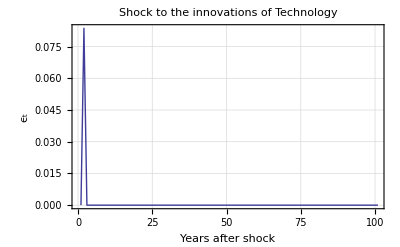

```mathematica
ssrbcmod202=ListLinePlot[ϵp2,FrameLabel->{"Years after shock","ϵ_t"},PlotLabel->"Shock to the innovations of Technology",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed]
```

Now we remind the equation of technology and calculate the impulse response function of technology.

```mathematica
ssrbcmod196
```

zh_t==0.95 zh_(-1+t)+ϵ_t

```mathematica
ssrbcmod203=fzh[0.95,ϵp2,99];
```

We plot the impulse response function of technology. The graph shows that technology starts from its steady-state value of 0 and increases in response to the shock of one standard deviation, and then gradually decreases towards its steady-state value.

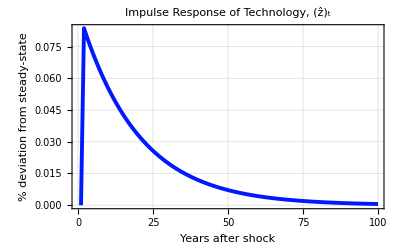

```mathematica
ssrbcmod204=ListLinePlot[ssrbcmod203,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Technology, (ẑ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.65]}]
```

We remind the equation of next period capital stock (kh_(t+1)) and calculate the impulse response function of capital stock (kh_t).

```mathematica
ssrbcmod197
```

kh_(1+t)==0.955782 kh_t+0.0991599 zh_t

```mathematica
ssrbcmod205=fkh[ssrbcmod197[[2,1,1]],ssrbcmod197[[2,2,1]],100,ssrbcmod203];
```

We plot the impulse response function of capital stock (kh_t). We see that the graph of the impulse response function of capital stock is hump-shaped.

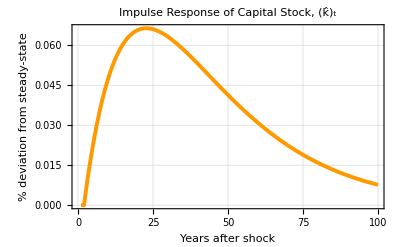

```mathematica
ssrbcmod206=ListLinePlot[ssrbcmod205,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Capital Stock, (k̂)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.1]}]
```

We remind the equation of consumption.

```mathematica
ssrbcmod198
```

ch_t==0.252683 kh_t+0.258221 zh_t

We calculate the impulse response function of consumption.

```mathematica
ssrbcmod207=fch[ssrbcmod198[[2,1,1]],ssrbcmod198[[2,2,1]],ssrbcmod205,ssrbcmod203];
```

We plot the impulse response function of consumption. Like the capital stock, we see that the graph of the impulse response function of consumption is hump-shaped.

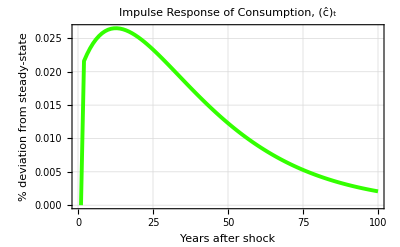

```mathematica
ssrbcmod208=ListLinePlot[ssrbcmod207,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Consumption, (ĉ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.3]}]
```

We remind the equation of labor.

```mathematica
ssrbcmod192
```

lh_t==-0.576882 kh_t+0.326575 zh_t

We calculate the impulse response function of labor.

```mathematica
ssrbcmod209=flh[ssrbcmod192[[2,1,1]],ssrbcmod192[[2,2,1]],ssrbcmod205,ssrbcmod203];
```

We plot the impulse response function of labor. We see that labor first augments and then decreases gradually, and increases again progressively to its steady-state level.

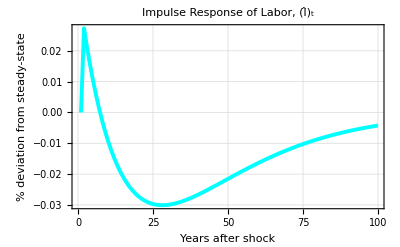

```mathematica
ssrbcmod210=ListLinePlot[ssrbcmod209,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Labor, (l̂)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.5]}]
```

We remind the equation of output.

```mathematica
ssrbcmod200
```

yh_t==-0.00920447 kh_t+1.20901 zh_t

We calculate the impulse response function of output.

```mathematica
ssrbcmod211=fyh[ssrbcmod200[[2,1,1]],ssrbcmod200[[2,2,1]],ssrbcmod205,ssrbcmod203];
```

We plot the impulse response function of output. As technology, we observe that output increases in response to the shock and then gradually falls to its steady-state level.

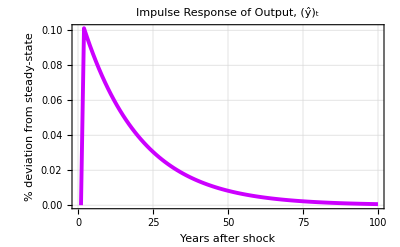

```mathematica
ssrbcmod212=ListLinePlot[ssrbcmod211,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Output, (ŷ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.8]}]
```

We remind the equation of investment.

```mathematica
ssrbcmod201
```

ivh_t==-0.768707 kh_t+3.9664 zh_t

We calculate the impulse response function of investment.

```mathematica
ssrbcmod213=fivh[ssrbcmod201[[2,1,1]],ssrbcmod201[[2,2,1]],ssrbcmod205,ssrbcmod203];
```

We plot the impulse response function of investment. As output, we see that investment rises in response to the shock and then progressively falls towards its steady-state level.

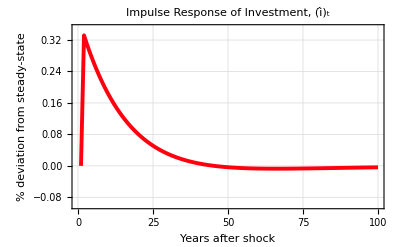

```mathematica
ssrbcmod214=ListLinePlot[ssrbcmod213,FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response of Investment, (î)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.007],Hue[0.99]},PlotRange->{{0,100},{-0.1,0.35}}]
```

Now we combine all these preceding figures into a single graph.

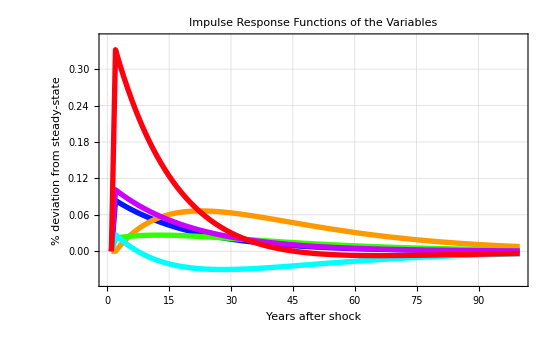

```mathematica
ssrbcmod215=ListLinePlot[{ssrbcmod203,ssrbcmod205,ssrbcmod207,ssrbcmod209,ssrbcmod211,ssrbcmod213},FrameLabel->{"Years after shock","% deviation from steady-state"},PlotLabel->"Impulse Response Functions of the Variables",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotLegend->{"Technology","Capital Stock","Consumption","Labor","Output","Investment"}, LegendPosition->{1.1,-0.4},ImageSize->550,PlotStyle->{{Thickness[0.007],Hue[0.65]},{Thickness[0.007],Hue[0.1]},{Thickness[0.007],Hue[0.3]},{Thickness[0.007],Hue[0.5]},{Thickness[0.007],Hue[0.8]},{Thickness[0.007],Hue[0.99]}},PlotRange->{{0,100},{-0.05,0.35}}]
```

Now we present the graphs side by side.

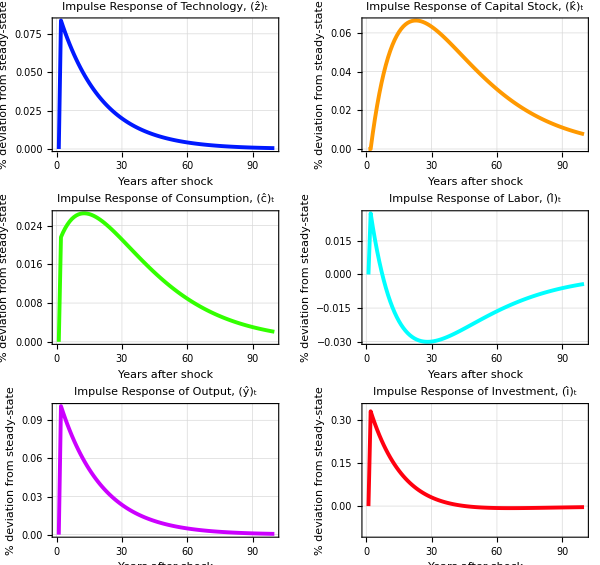

```mathematica
ssrbcmod216=GraphicsGrid[{{ssrbcmod204,ssrbcmod206},{ssrbcmod208,ssrbcmod210},{ssrbcmod212,ssrbcmod214}},ImageSize->600]
```

## 5.2. Stochastic Simulation

We set the random seed to 2000 in order to allow the reproduction of our simulations.

```mathematica
SeedRandom[2000]
```

We generate 5000 normal random numbers with mean 0 and standard deviation 0.083666. This series represents the innovations to technology.

```mathematica
ssrbcmod217=RandomVariate[NormalDistribution[0,0.083666],5000];
```

Now we plot only the last 150 values of the previous series.

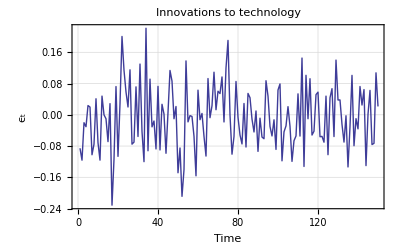

```mathematica
ssrbcmod218=ListLinePlot[Take[ssrbcmod217,-150],FrameLabel->{"Time",Subscript[ϵ, t]},PlotLabel->"Innovations to technology",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed]
```

Next we present the Hodrick-Prescott (1997) filter used to filter the data we are going to study. To find the Hodrick-Prescott (HP) filter, we minimize the following expression:

Min_((g_t)_(t=1)^T)∑_(t=1)^T c_t^2+λ ∑_(t=3)^T [(g_t-g_(t-1))-(g_(t-1)-g_(t-2))]^2

Subject to:

  c_t=y_t-g_t

Where y_t is the series we want to smooth, g_t is the trend component, c_t is the cyclical component and λ is the smoothing parameter. 
Danthine and Girardin (1989) show that the solution to this optimization problem is given by:

g_t=(I+λ K' K)^-1 y_t

With I an identity matrix of dimension T and K is a special matrix of dimension (T-2)×T having the following form:

(1
0
0
⋮
0-2
1
0
⋮
01
-2
1
⋮
00
1
-2
⋮
00
0
1
⋮
0⋯
⋯
⋯
⋯
⋯0
0
0
⋮
10
0
0
⋮
-20
0
0
⋮
1)

Having found g_t, the the cyclical component is calculated as  c_t=y_t-g_t. Since the parameters of our model are calibrated for quarterly data, we will use the value λ = 1600. Now let us write a function that computes the HP filter. The function takes two arguments: the first is the data we want to smooth and the second is the value of the parameter λ. The function then returns the cyclical component and the trend component respectively.

```mathematica
hPfilterz[data_List,λ_?Positive]:=Module[{totime,trend,cycle,KKMAT,IDM,MATA},totime=Length[data];KKMAT=SparseArray[
    {{r_, r_} -> 1.,{r_, s_} /; s == r + 1 -> -2.,{r_, s_} /; s == r + 2 -> 1.}, {(totime - 2), totime},0.];IDM=IdentityMatrix[totime];MATA=IDM+λ Transpose[KKMAT].KKMAT ;trend = LinearSolve[MATA, data,Method->"Automatic"];cycle=data-trend;{cycle,trend}]
```

We generate the simulated time series of technology.

```mathematica
ssrbcmod219=fzh[0.95,ssrbcmod217,4999];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod220=Take[ssrbcmod219,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod221=hPfilterz[ssrbcmod220,1600];
```

We extract the cyclical component of the technology series.

```mathematica
ssrbcmod222=ssrbcmod221[[1]];
```

We plot the HP-filtered time path of technology.

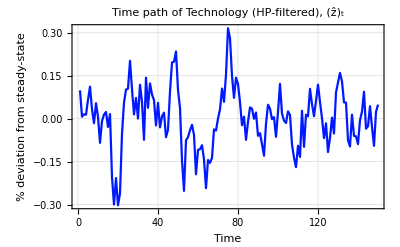

```mathematica
ssrbcmod223=ListLinePlot[ssrbcmod222,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Technology (HP-filtered), (ẑ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.65]}]
```

We generate the simulated time series of capital stock.

```mathematica
ssrbcmod224=fkh[ssrbcmod197[[2,1,1]],ssrbcmod197[[2,2,1]],5000,ssrbcmod219];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod225=Take[ssrbcmod224,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod226=hPfilterz[ssrbcmod225,1600];
```

We extract the cyclical component of the capital stock series.

```mathematica
ssrbcmod227=ssrbcmod226[[1]];
```

We plot the HP-filtered time path of capital stock.

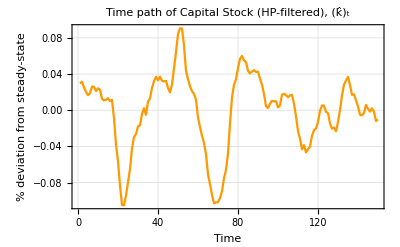

```mathematica
ssrbcmod228=ListLinePlot[ssrbcmod227,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Capital Stock (HP-filtered), (k̂)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.1]}]
```

We generate the simulated time series of consumption.

```mathematica
ssrbcmod229=fch[ssrbcmod198[[2,1,1]],ssrbcmod198[[2,2,1]],ssrbcmod224,ssrbcmod219];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod230=Take[ssrbcmod229,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod231=hPfilterz[ssrbcmod230,1600];
```

We extract the cyclical component of the consumption series.

```mathematica
ssrbcmod232=ssrbcmod231[[1]];
```

We plot the HP-filtered time path of consumption.

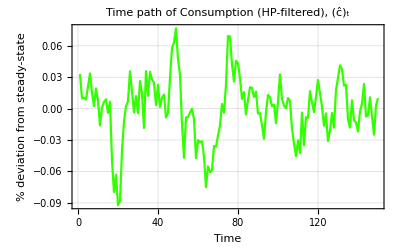

```mathematica
ssrbcmod233=ListLinePlot[ssrbcmod232,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Consumption (HP-filtered), (ĉ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.3]}]
```

We generate the simulated time series of labor.

```mathematica
ssrbcmod234=flh[ssrbcmod192[[2,1,1]],ssrbcmod192[[2,2,1]],ssrbcmod224,ssrbcmod219];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod235=Take[ssrbcmod234,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod236=hPfilterz[ssrbcmod235,1600];
```

We extract the cyclical component of the labor series.

```mathematica
ssrbcmod237=ssrbcmod236[[1]];
```

We plot the HP-filtered time path of labor.

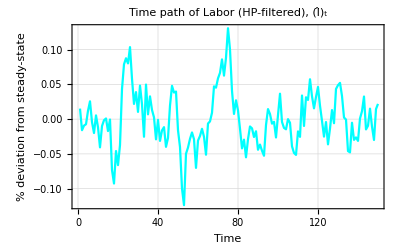

```mathematica
ssrbcmod238=ListLinePlot[ssrbcmod237,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Labor (HP-filtered), (l̂)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.5]}]
```

We generate the simulated time series of output.

```mathematica
ssrbcmod239=fyh[ssrbcmod200[[2,1,1]],ssrbcmod200[[2,2,1]],ssrbcmod224,ssrbcmod219];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod240=Take[ssrbcmod239,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod241=hPfilterz[ssrbcmod240,1600];
```

We extract the cyclical component of the output series.

```mathematica
ssrbcmod242=ssrbcmod241[[1]];
```

We plot the HP-filtered time path of output.

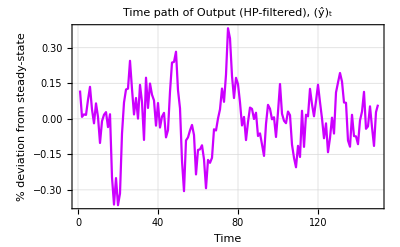

```mathematica
ssrbcmod243=ListLinePlot[ssrbcmod242,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Output (HP-filtered), (ŷ)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.8]}]
```

We generate the simulated time series of investment.

```mathematica
ssrbcmod244=fivh[ssrbcmod201[[2,1,1]],ssrbcmod201[[2,2,1]],ssrbcmod224,ssrbcmod219];
```

We take the last 150 values of the previous series.

```mathematica
ssrbcmod245=Take[ssrbcmod244,-150];
```

We apply the HP-filter to the preceding result.

```mathematica
ssrbcmod246=hPfilterz[ssrbcmod245,1600];
```

We extract the cyclical component of the investment series.

```mathematica
ssrbcmod247=ssrbcmod246[[1]];
```

We plot the HP-filtered time path of investment.

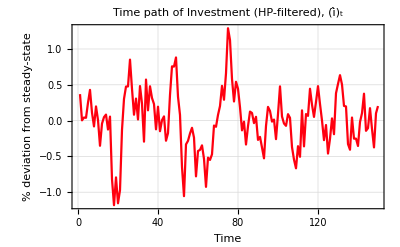

```mathematica
ssrbcmod248=ListLinePlot[ssrbcmod247,FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of Investment (HP-filtered), (î)_t",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotStyle->{Thickness[0.004],Hue[0.99]}]
```

Now we combine all these preceding figures into a single graph.

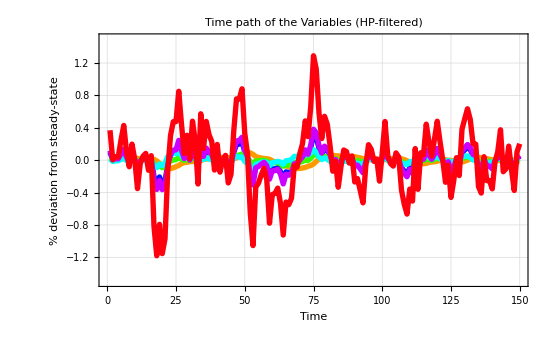

```mathematica
ssrbcmod249=ListLinePlot[{ssrbcmod222,ssrbcmod227,ssrbcmod232,ssrbcmod237,ssrbcmod242,ssrbcmod247},FrameLabel->{"Time","% deviation from steady-state"},PlotLabel->"Time path of the Variables (HP-filtered)",Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotLegend->{"Technology","Capital Stock","Consumption","Labor","Output","Investment"}, LegendPosition->{1.1,-0.4},ImageSize->550,PlotStyle->{{Thickness[0.007],Hue[0.65]},{Thickness[0.007],Hue[0.1]},{Thickness[0.007],Hue[0.3]},{Thickness[0.007],Hue[0.5]},{Thickness[0.007],Hue[0.8]},{Thickness[0.007],Hue[0.99]}},PlotRange->{{0,150},{-1.5,1.5}}]
```

The graph illustrates that investment is more volatile than output while capital stock and consumption are smoother than output.

Now we present the graphs side by side.

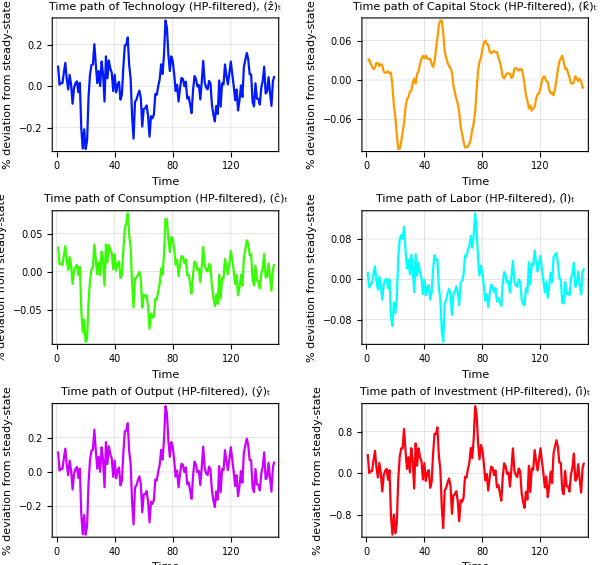

```mathematica
ssrbcmod250=GraphicsGrid[{{ssrbcmod223,ssrbcmod228},{ssrbcmod233,ssrbcmod238},{ssrbcmod243,ssrbcmod248}},ImageSize->600]
```

## 5.3. Second Moments Statistics

We start by writing a function that calculates the relative standard deviation. The function takes two arguments. Both arguments are lists or time series in our case. The result of the function is the standard deviation of the first series relative to the second.

```mathematica
relativesd[mvar_List,output_List]:=Module[{sdmvar,sdout},sdmvar=StandardDeviation[mvar];sdout=StandardDeviation[output];sdmvar/sdout]
```

We compute the standard deviation of each series relative output. To do this we automate the process by creating a function that takes as first argument a list of list containing the series and as second argument the output series. The function then gives as result the list of the relative standard deviations.

```mathematica
listrsdfunct[listrsd_,outrsd_]:=Module[{res1,NN},NN=Length[listrsd];res1=Table[0,{i,NN}];Do[res1[[i]]=relativesd[listrsd[[i]],outrsd],{i,1,NN}];res1]
```

We enter the series for which we want to calculate the relative standard deviation with output.

```mathematica
ssrbcmod251={ssrbcmod222,ssrbcmod227,ssrbcmod232,ssrbcmod237,ssrbcmod247};
```

We calculate the relative standard deviation of technology, capital stock, consumption, labor and investment respectively with output.

```mathematica
ssrbcmod252=listrsdfunct[ssrbcmod251,ssrbcmod242]
```

{0.827272,0.325121,0.233494,0.319369,3.27558}

We create a function that compute the correlation of each series with output. The function takes as first argument a list of list containing the series and as second argument the output series. The result of the function is a list containing the correlation of each series with output.

```mathematica
listcorrfunct[listcorr_,outcorr_]:=Module[{rescorr,NNC},NNC=Length[listcorr];rescorr=Table[0,{i,NNC}];Do[rescorr[[i]]=Correlation[listcorr[[i]],outcorr],{i,1,NNC}];rescorr]
```

We compute the correlation of technology, capital stock, consumption, labor and investment respectively with output.

```mathematica
ssrbcmod253=listcorrfunct[ssrbcmod251,ssrbcmod242]
```

{0.999996,0.0579083,0.935252,0.811926,0.997319}

We display the relative standard deviation next to the correlation.

```mathematica
ssrbcmod254=Transpose[{ssrbcmod252,ssrbcmod253}]
```

{{0.827272,0.999996},{0.325121,0.0579083},{0.233494,0.935252},{0.319369,0.811926},{3.27558,0.997319}}

Now we display the Second Moments Statistics of the model in table form.

```mathematica
ssrbcmod255=TableForm[ssrbcmod254,TableHeadings->{{"Technology","Capital Stock","Consumption","Labor", "Investment"},{"relative volatility","correlation"}},TableAlignments->Center]
```

| relative volatility | correlation
Technology | 0.827272 | 0.999996
Capital Stock | 0.325121 | 0.0579083
Consumption | 0.233494 | 0.935252
Labor | 0.319369 | 0.811926
Investment | 3.27558 | 0.997319

From this table it appears that consumption, labor and capital stock are less volatile than output. Technology is almost as volatile as output. Investment is more volatile than output. The table also illustrates that technology, investment and consumption are highly procyclic, while capital stock is less correlated with output.

## 6. Conclusion

This notebook has demonstrated how to solve and simulate a Real Business Cycle (RBC) model using the software Mathematica. We have also shown how to find the first order conditions, derive the steady-state and log-linearize the model. A good extension of this notebook could be:

First, to automate some parts instead of doing it step by step.We have chosen this last method for pedagogic reasons.

Second, to use alternatives solution methods.

## 7. References

Barro, R. J. and X. Sala-i-Martin: 2004, Economic Growth, Second Edition, MIT Press.

Danthine, J. P. and M. Girardin: 1989, Business cycles in switzerland, a comparative study, European Economic Review, 33, 31-50.

Hansen, G. D.: 1985, Indivisible labor and the business cycle, Journal of Monetary Economics, 16(3), 309-327.

Hartley, J. E., K. D. Hoover and K. D. Salyer: 1998, A user’s guide to solving real business cycle models, In Real business cycles, A Reader, pp: 43-54, Routledge, London and New York.

Hodrick, R. J. and E. C. Prescott: 1997, Post-war U.S. business cycles: an empirical investigation, Journal of Money, Credit and Banking, 29(1), 1-16.

Mandelman, F. S. and F. Zanetti: 2008, Estimating general equilibrium models: an application with labour market frictions, Technical Handbook-No.1, Centre for Central Banking Studies, Bank of England.

Uhlig, H.: 1997, A toolkit for analyzing nonlinear dynamic stochastic models easily, Working Paper, Center, University of Tilburg.

Zietz, J.: 2008, A clarifying note on converting to log-deviations from the steady state, Economics Bulletin, 3(50), 1-15.